```mathematica
Quit[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
sp0=Import["sp0.txt","Table"];
sp1=Import["sp1.txt","Table"];
n0 = (Length@sp0+1)/3;
n1 = (Length@sp1+1)/3;
cx=Join[sp0⟦1;;n0⟧,sp1⟦1;;n1⟧];
cy=Join[sp0⟦n0+1;;n0*2⟧,sp1⟦n1+1;;n1*2⟧];
h=Join[sp0⟦2 n0+1;;-1⟧,sp1⟦2n1+1;;-1⟧];
(*Length@data*)
Subscript[sx, i_][t_?NumberQ]:=cx⟦i,1⟧+cx⟦i,2⟧t+(cx⟦i,3⟧t^2+cx⟦i,4⟧t^3+cx⟦i,5⟧t^4+cx⟦i,6⟧t^5)
Subscript[sy, i_][t_?NumberQ]:=cy⟦i,1⟧+cy⟦i,2⟧t+(cy⟦i,3⟧t^2+cy⟦i,4⟧t^3+cy⟦i,5⟧t^4+cy⟦i,6⟧t^5)
{x[t_],y[t_]}=50(1+0.05Cos[8t-π]){Sin[t],Cos[t]};
Table[{Subscript[sx, i][t],Subscript[sy, i][t]},{i,1,Length@cx-1}];
Show[
ListPlot[Transpose[{cx⟦1;;-1,1⟧,cy⟦1;;-1,1⟧}]]
(*,ParametricPlot[{x[t],y[t]},{t,0,π},PlotStyle->Red]*)
,ParametricPlot[{%⟦1;;n0-1;;2⟧,%⟦2;;n0-1;;2⟧},{t,0,1},AspectRatio->Automatic]
,AspectRatio->Automatic,ImageSize->Medium]
```

$Aborted

```mathematica
"
```

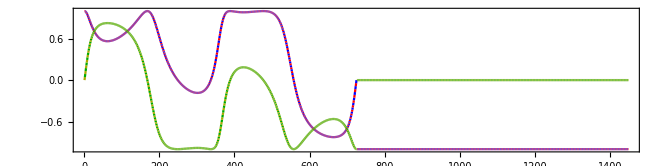

```mathematica
dv=1;
tx = Table[Flatten@{(#+i),Derivative[dv][Subscript[sx, i]][#]/h⟦i⟧^dv}&/@Range[0.0,1,0.1],{i,Join[Range[1,n0-1],Range[n0+1,n0+n1 -2]]}];
ty = Table[Flatten@{#+i,Derivative[dv][Subscript[sy, i]][#]/h⟦i⟧^dv}&/@Range[0.0,1,0.1],{i,Join[Range[1,n0-1],Range[n0+1,n0+n1 -2]]}];
(*ty = Table[{t+i,Derivative[dv][Subscript[sy, i]][t]/h⟦i⟧^dv},{i,1,Length@cx-1}];*)
Show[
ListPlot[tx,PlotStyle->{Red,Blue},Joined->True,PlotRange->All],
ListPlot[ty,PlotStyle->Darker@{Yellow,Green},Joined->True,PlotRange->All],
(*ParametricPlot[{ty⟦1⟧,ty⟦2⟧},{t,0,1}],*)
AspectRatio->0.25,Frame->True]
```

```mathematica
n0
```

23

```mathematica
(p[t])⟦1⟧
```

(1+0.2 Cos[8 t]) Sin[t]

{-0.00128027,0.00137097,-0.00103588,-0.00014208,-0.000723287,0.000896066,0.000896066,-0.000723287,-0.00014208,-0.00103588,0.00137097}

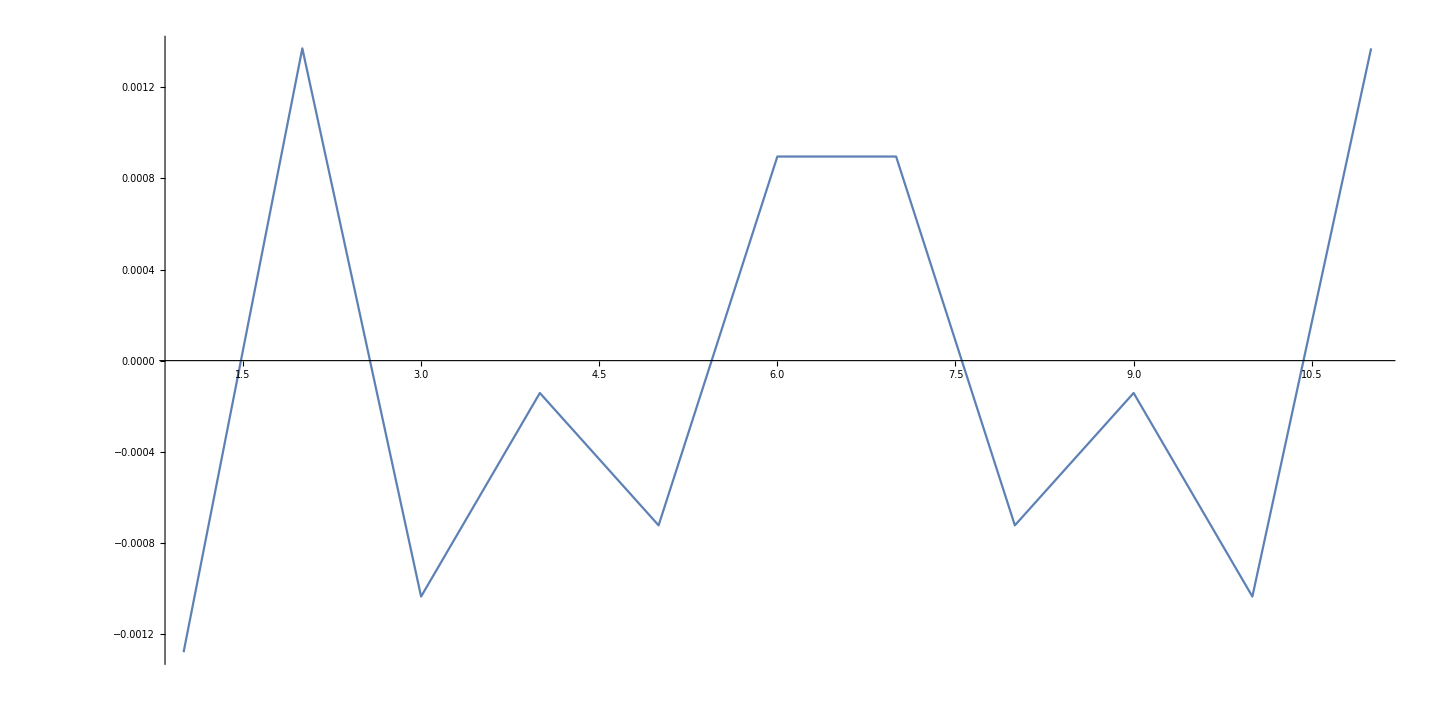

```mathematica
Clear[i,kv,kvt]
θ=Table[ArcCos[Subscript[sy, i][0]/√((Subscript[sx, i][0])^2+ (Subscript[sy, i][0])^2)],{i,1,Length@cx}];//Quiet;
Subscript[kv, i_][t_]:=(Subscript[sx, i]'[t]Subscript[sy, i]''[t]-Subscript[sy, i]'[t]Subscript[sx, i]''[t])/((Subscript[sx, i]'[t])^2+(Subscript[sy, i]'[t])^2)^1.5
kvt[t_]:=(x'[t]y''[t]-y'[t]x''[t])/(x'[t]^2+y'[t]^2)^1.5
Table[Subscript[kv, i][0.]-Evaluate@kvt[θ⟦i⟧],{i,1,n0-1 }]
Show[ListPlot[%,PlotRange->All,Joined->True],AspectRatio->0.5,PlotRange->All]
```

```mathematica
6.219718254214801*^-7
```

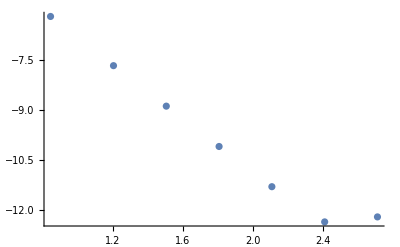

FittedModel[-3.59043-3.462 x]

```mathematica
dd={{7,6.219718254214801*^-7},
{16,2.1043927281305663*^-8},
{32,1.2964614815730302*^-9},
{64,8.074397574164838*^-11},
{128,5.0717728627969194*^-12},
{256,4.4955358879938956*^-13},
{512,6.340639818747107*^-13}
};
ListPlot@Log10@dd
LinearModelFit[Log10@dd,{x},x]
```

```mathematica
386*4
```

1544